## Partial wave expantion of the Exponenta

```mathematica
Block[{k={1.34,1.67,0.56},r={0.45,0.82,0.91},E1,E2},
E1=Exp[-ⅈ k.r];
E2=Sum[ⅈ^(2+L)(2L+1)SphericalBesselJ[L,Norm@k   Norm@r]LegendreP[L,(k.r)/((Norm@k) Norm@r)],{L,0,15}];
{E1,E2}
]
```

{-0.790242-0.612795 ⅈ,0.790242-0.612795 ⅈ}

## A Fourier Transform

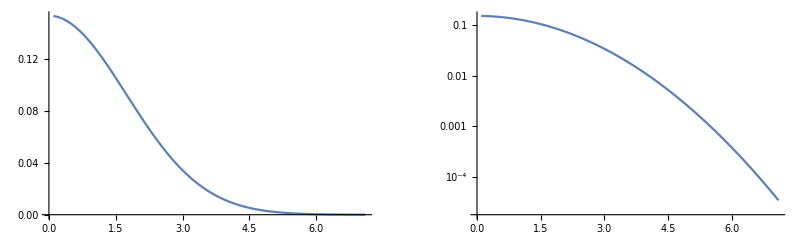

```mathematica
Block[{alphaDD,corrDD,Q={Qr,Qth,Qph},ρ,R={2.45,Rth,Rph},sphR,aGamma1=1/2,
aGamma2 =1/4,aGamma0,,E1,E2,E3,R0=2.45,qAlphaDD ,qCorrDD,graph1,graph2},
alphaDD[r_]:=(Pi/aGamma1)^(-3/2)Exp[- aGamma1 r.r];
corrDD[r_]:=(Pi/aGamma2)^(-3/2)Exp[-aGamma2 r.r];
qAlphaDD[qx_]:=Exp[-1/(4aGamma1) qx^2];
qCorrDD[qx_]:=Exp[-1/(4aGamma2) qx^2];
E1=Hold@NIntegrate[
Qr^2 Sin[Qth]Sin[Rth]
alphaDD[FromSphericalCoordinates[R]-FromSphericalCoordinates[Q]]
corrDD[{Q⟦1⟧,0,0}]
,{Qr,0,Infinity},{Qth,0,Pi},{Qph,0,2Pi},{Rth,0,Pi},{Rph,0,2Pi}];
E2=   Hold@Integrate[SphericalBesselJ[0,q #] q^2 qAlphaDD[q]qCorrDD[q],{q,0,Infinity}]&[R0];
E3=4 Pi^(-1/2)((aGamma1 aGamma2)/(aGamma1 +aGamma2))^(3/2)Exp[- (aGamma1 aGamma2)/(aGamma1 +aGamma2) #^2]&/@Range[0.1,7.1,0.1];
graph1=ListPlot[Transpose[{Range[0.1,7.1,0.1],E3}],Joined->True];graph2=ListLogPlot[Transpose[{Range[0.1,7.1,0.1],E3}],Joined->True];
GraphicsRow[{graph1,graph2}]
]
```

```mathematica
FourierTransform[x^(2+2λ)Exp[-aij x^2],x,q]
```

1/(√(2 π))aij^(-2-λ) ⅇ^(ⅈ π λ) (√aij Cos[π λ] Gamma[3/2+λ] Hypergeometric1F1[3/2+λ,1/2,-q^2/(4 aij)]+q Gamma[2+λ] Hypergeometric1F1[2+λ,3/2,-q^2/(4 aij)] Sin[π λ])